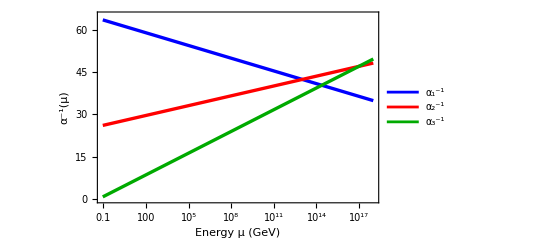

```mathematica
MZ=91.1876;
alpha1Inv[mu_]:=59-(41/(20 Pi)) Log[mu/MZ]
alpha2Inv[mu_]:=29.6-((-19/6)/(2 Pi)) Log[mu/MZ]
alpha3Inv[mu_]:=8.5-((-7)/(2 Pi)) Log[mu/MZ]

(*定義常數*)MZ=91.1876;
alpha1Inv[mu_]:=59-(41/(20 Pi)) Log[mu/MZ]
alpha2Inv[mu_]:=29.6-((-19/6)/(2 Pi)) Log[mu/MZ]
alpha3Inv[mu_]:=8.5-((-7)/(2 Pi)) Log[mu/MZ]

(*繪圖*)
Plot[{alpha1Inv[mu],alpha2Inv[mu],alpha3Inv[mu]},{mu,MZ/1000,10^18},
BaseStyle->{FontSize->20,FontFamily->"Arial"},
PlotRange->{0,65},ScalingFunctions->{"Log",None},PlotLegends->{Style["\!\(\*SubscriptBox[\(α\), \(1\)]\)\!\(\*SuperscriptBox[\(\), \(-1\)]\)",20],Style["\!\(\*SubscriptBox[\(α\), \(2\)]\)\!\(\*SuperscriptBox[\(\), \(-1\)]\)",20],Style["\!\(\*SubscriptBox[\(α\), \(3\)]\)\!\(\*SuperscriptBox[\(\), \(-1\)]\)",20]},
Frame->True,
FrameLabel->{Style["Energy μ (GeV)",FontSize->20,Bold],Style["\!\(\*SuperscriptBox[\(α\), \(-1\)]\)(μ)",FontSize->20,Bold]},
PlotStyle->{{Blue,Thickness->0.006},{Red,Thickness->0.006},{Darker[Green],Thickness->0.006}},GridLines->Automatic,ImageSize->Full,AspectRatio->0.6]
```

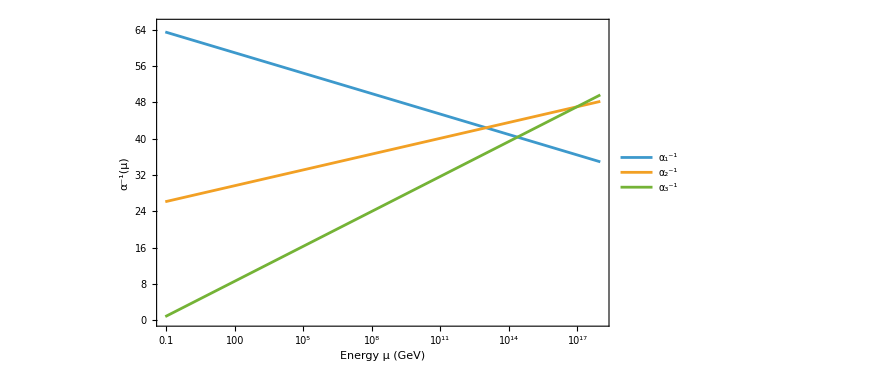

```mathematica
Plot[{alpha1Inv[mu],alpha2Inv[mu],alpha3Inv[mu]},{mu,MZ/1000,10^18},BaseStyle->{FontSize->20,FontFamily->"Arial"},PlotRange->{0,65},ScalingFunctions->{"Log",None},PlotLegends->{Style["\!\(\*SubscriptBox[\(α\), \(1\)]\)\!\(\*SuperscriptBox[\(\), \(-1\)]\)",24,Black,Bold],Style["\!\(\*SubscriptBox[\(α\), \(2\)]\)\!\(\*SuperscriptBox[\(\), \(-1\)]\)",24,Black,Bold],Style["\!\(\*SubscriptBox[\(α\), \(3\)]\)\!\(\*SuperscriptBox[\(\), \(-1\)]\)",24,Black,Bold]},Frame->True,FrameLabel->{Style["Energy μ (GeV)",20,Bold,Black],Style["\!\(\*SuperscriptBox[\(α\), \(-1\)]\)(μ)",20,Bold,Black]},GridLines->Automatic,ImageSize->Full,AspectRatio->0.6
]
```

```mathematica
6.25*10^(62)*6.58*10^(-25)/86400/365
```

1.30407×10^31